# CARBAPENEM RESISTANCE MODEL

## Data

### Preparing Directory

Clear all variables. Set directory and change setting such that when it closes it closes all outputs.

```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];
SetOptions[EvaluationNotebook[],NotebookEventActions->{"WindowClose":>FrontEndExecute[FrontEndToken["DeleteGeneratedCells"]]}];
```

### Load Data

Reading country data on consumption and resistance and assigning them to appropriate variables.

```mathematica
countryname="US_DDD"; 
data=Import["DataSheet_cddep.xlsx",{"Data",countryname}];
data = data[[All,2;;]];
years = data[[1]];
tt = Length[years]; 
nop = (Length[data]-5)/2; (*# of pathogens*)
isolates = data[[2;;Length[data]-4;;2]];
resistance = data[[3;;Length[data]-4;;2]];
rfreq =resistance/isolates;
carbcons =  data[[-1]];
conbreak = data[[-3,1;;nop]]; (*CBP consumption for KP, PA, AB*)
cbp =data[[-2,1]]*Table[carbcons*conbreak[[i]],{i,1,nop}];
```

## Model

### Parameters & Model Structure

r(t) = frequency of resistance
k_s= natural growth rate of the sensitive strain
k_r= natural growth rate of the resistance strain (k_r < k_s)
θ = k_r-k_s< 0 
a = CBP consumption (DDD)

```mathematica
r[t_,r0_,ks_,θ_]:=ⅇ^(Total[ks*a[[1;;t]]]+θ*t)/((1/r0)-1+ⅇ^(Total[ks*a[[1;;t]]]+ θ*t));
```

### Likelihood

```mathematica
Lik[r0_,ks_,θ_]:= Total[Table[Log[Binomial[iso[[j]],resis[[j]]]]+resis[[j]]*Log[r[j-1,r0,ks,θ]]+(iso[[j]]-resis[[j]])*Log[1-r[j-1,r0,ks,θ]],{j,1,tt}]]
```

```mathematica
Likelihood Surface
i = 3;
iso = isolates[[i]]
resis = resistance[[i]]
a = cbp[[i]]
loglik[r0_,ks_]:=Total[Table[Log[Binomial[iso[[j]],resis[[j]]]]+resis[[j]]*Log[r[j-1,r0,ks,-0.1]]+(iso[[j]]-resis[[j]])*Log[1-r[j-1,r0,ks,-0.1]],{j,1,tt}]]
Plot3D[loglik[r0,ks],{r0,0,0.1},{ks,700,1000}]
```

Likelihood Surface

{681.,887.,955.,998.,1187.,1143.,890.,860.,757.,603.,419.,365.,163.,831.,738.}

{61.29,124.18,191.,179.64,213.66,262.89,186.9,301.,295.23,301.5,184.36,135.05,70.09,448.74,361.62}

{0.000956634,0.00113868,0.00139308,0.00144023,0.00155998,0.00171756,0.00191485,0.00200609,0.00217244,0.00230301,0.0023598,0.00249113,0.00254821,0.00233718,0.00247134}

-Graphics3D-

### Model Fitting

```mathematica
max  = PadRight[{},nop,Null];
fr0 = max; fks=max; fθ=max;
For[i=1,i≤nop,i++,{iso=isolates[[i]],resis = resistance[[i]],a = cbp[[i]],{max[[i]],{fr0[[i]],fks[[i]],fθ[[i]]}}=NMaximize[{Lik[r0,ks,θ],0<r0<1,θ<-0.1},{r0,ks,θ}, MaxIterations->100000]}]

fr0 = Table[fr0[[i]][[2]],{i,1,nop}];
fks = Table[fks[[i]][[2]],{i,1,nop}] ;
fθ=Table[fθ[[i]][[2]],{i,1,nop}];

(*create table of fitted values*)
params= Join[{max},{fr0},{fks},{fθ}];
headings1=Prepend[params,{"KP","PA","AB","EA/C"}];
headings2=MapThread[Prepend,{headings1,{"","Likelihood","r0","k_s","θ"}}];
Grid[headings2,Frame-> All]
```

| KP | PA | AB | EA/C
Likelihood | -338.471 | -120.611 | -160.27 | -113.668
r0 | 0.00618264 | 0.187208 | 0.171297 | 0.000773001
k_s | 112.653 | 24.2885 | 127.527 | 223.918
θ | -0.1 | -0.1 | -0.1 | -0.1

```mathematica
Sampling
```

Sampling

```mathematica
fr0[[1]]
```

0.00618264

```mathematica
i = 4;
iso = isolates[[i]];
resis = resistance[[i]];
a = cbp[[i]];
loglik[r0_,ks_]:=Total[Table[Log[Binomial[iso[[j]],resis[[j]]]]+resis[[j]]*Log[r[j-1,r0,ks,-0.1]]+(iso[[j]]-resis[[j]])*Log[1-r[j-1,r0,ks,-0.1]],{j,1,tt}]];
fonGrid[x_,y_,f_]:=Module[{n,m,fvals},
(*x is an n-by-1 vector*)
(*y is an n-by-1 vector*)
(*f is a scalar function of two variables*)
(*fvals is an m-by-n matirx where fVals[[i,j]]=f[x[[j]],y[[i]]]*)
n=Length[x];
m=Length[y];
fvals=Table[0,{m},{n}];(*preallocate fvals*)Do[Do[fvals[[i,j]]=f[x[[j]],y[[i]]];,{i,1,m}];,{j,1,n}];
fvals]
```

```mathematica
x = RandomReal[{0.9*fr0[[i]],1.1*fr0[[i]]},100];
y = RandomReal[{0.9*fks[[i]],1.1*fks[[i]]},100];
ld = fonGrid[x,y,loglik];
d = Exp[ld];
w = d/Total[Total[d]];
ds =ArrayReshape[d,{1,100*100}][[1]];
ws = ArrayReshape[w,{1,100*100}][[1]];
repeat[m_,n_Integer?Positive]:=Sequence@@ConstantArray[m,n]
xs = Table[repeat[x[[i]],100],{i,1,100}];
ys = PadRight[y,10000,y];
rs = RandomChoice[ws->Range[10000],1000];
xs = xs[[rs]]; ys = ys[[rs]]; ds = ds[[rs]];
```

#### Plots

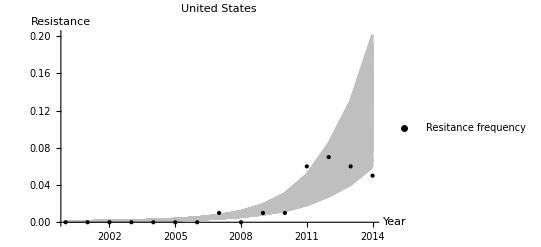

```mathematica
t=Range[1,tt]; 
i =4;
xp =PadRight[{},1000,Null];
res = Transpose@{years,rfreq[[i]]}; (*resistance frequency data*)
For[j=1,j≤1000,j++,{iso=isolates[[i]],resis = resistance[[i]],a = cbp[[i]],xp[[j]]= Table[r[k,xs[[j]],ys[[j]],-0.1],{k,1,tt}]}];
fit = Table[Transpose@{years,xp[[i]]},{i,1,1000}];
plotD = ListPlot[res,PlotStyle->{{Black,PointSize[Large]}},PlotRange->All,PlotLegends->{"Resitance frequency"}];
plotM =ListLinePlot[Table[fit[[j]],{j,1000}],PlotStyle->RGBColor[0.75,0.75,0.75],AxesLabel->{Year,Resistance},PlotRange->All,PlotLabel->"United States",PlotLegends->"Model fit"];
Show[{plotM,plotD},PlotRange->All]
```

```mathematica
t=Range[1,tt]; 
res = Table[Transpose@{years,rfreq[[i]]},{i,1,nop}]; (*resistance frequency data*)
x  = PadRight[{},nop,Null];
For[i=1,i≤nop,i++,{iso=isolates[[i]],resis = resistance[[i]],a = cbp[[i]],x[[i]] = Table[r[j,fr0[[i]],fks[[i]],fθ[[i]]],{j,1,tt}]}];
fit =  Table[Transpose@{years,x[[i]]},{i,1,nop}];

plotD = Table[ListPlot[{res[[i]]},PlotStyle->{{Black,PointSize[Large]}},PlotRange->All,PlotLegends->{"Resitance frequency"}],{i,1,nop}];
plotM = Table[ListLinePlot[{fit[[i]]},PlotStyle->RGBColor[0.75,0.75,0.75], AxesLabel->{Year,Resistance},PlotRange->All,PlotLabel->"United States",PlotLegends->{"Model fit"}],{i,1,nop}];
Show[plotD[[1]],plotM[[1]],PlotRange->All,PlotLabel->"United States (KP)"] ;
Show[plotD[[2]],plotM[[2]],PlotRange->All,PlotLabel->"United States (PA)"];
Show[plotD[[3]],plotM[[3]],PlotRange->All,PlotLabel->"United States (AB)"];
Show[plotD[[4]],plotM[[4]],PlotRange->All,PlotLabel->"United States (EA/C)"];
```

## Projections

### Status Quo & Interventions

```mathematica
cbp0 = data[[-2,1]]*carbcons[[-1]];  (*current CBP consumption*)
ti=years[[-1]]; (*projectsion begin at year Subscript[t, i]*)
tf =2030; (*projection until year Subscript[t, f]*) 
nyears = tf -ti;(*# of years to project across*)
pyears = Range[ years[[-1]],tf];
```

```mathematica
(*Status Quo: maintain current CBP consumption*)
projSQ =ConstantArray[cbp0,Round[nyears]];
cbpSQ = Table[Join[cbp[[i]],projSQ*conbreak[[i]]],{i,1,nop}];
```

```mathematica
(*Interventions:
(0) sparing1: 0 consumption at Subscript[t, i]
(1) sparing2: linear reduction to 0 consumption by Subscript[t, f]
(2) stewardship1: immediate reduction to a % of current consumption
(3) stewardship2: linear reduction to the a % of current consumption *) 

intv = 0.4; (*reduce current carbapenem consumption by (1-intv) % in next npy years linearly*)

option = 1; (*select 0-3; see above*)
If[option==0, projI = ConstantArray[0,Round[nyears]], 
If[option==1,projI = Range[cbp0,0,(-1)*cbp0/(nyears-1)], 
If[option==2, projI=ConstantArray[intv*cbp0,Round[nyears]], 
If[option == 3, projI = Range[cbp0,intv*cbp0,cbp0*(intv-1)/(nyears-1)]]]]];
cbpI = Table[Join[cbp[[i]], projI*conbreak[[i]]],{i,1,nop}];
```

```mathematica
(*Status Quo resistance frequency*)
y  = PadRight[{},nop,Null];
For[i=1,i≤nop,i++,{iso=isolates[[i]],resis = resistance[[i]],a = cbpSQ[[i]],y[[i]] = Table[r[j,fr0[[i]],fks[[i]],fθ[[i]]],{j,tt,tt+nyears}]}];
rSQ =  Table[Transpose@{pyears,y[[i]]},{i,1,nop}];
```

```mathematica
(*Intervention resistance frequency*)
z  = PadRight[{},nop,Null];
For[i=1,i≤nop,i++,{iso=isolates[[i]],resis = resistance[[i]],a = cbpI[[i]],z[[i]] = Table[r[j,fr0[[i]],fks[[i]],fθ[[i]]],{j,tt,tt+nyears}]}];
rI =  Table[Transpose@{pyears,z[[i]]},{i,1,nop}];
```

### Projection Plots

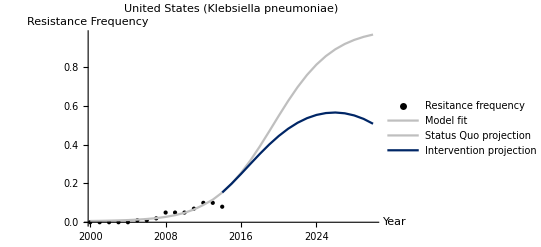

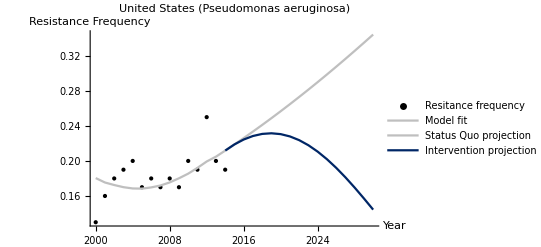

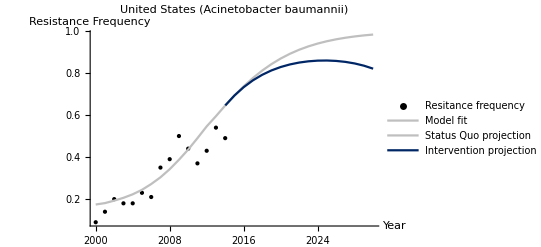

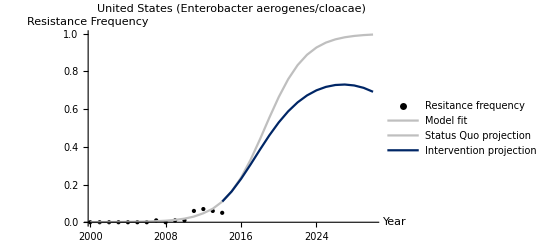

```mathematica
plotPSQ = Table[ListLinePlot[{rSQ[[i]]},PlotStyle->RGBColor[0.75,0.75,0.75],AxesLabel->{Year,Resistance},PlotRange->All,PlotLabel->"United States",PlotLegends->{"Status Quo projection"}],{i,1,nop}];
plotPI = Table[ListLinePlot[{rI[[i]]},PlotStyle->RGBColor[0,0.15,0.4],AxesLabel->{Year,Resistance},PlotRange->All,PlotLabel->"United States",PlotLegends->{"Intervention projection"}],{i,1,nop}];
Show[plotD[[1]],plotM[[1]],plotPSQ[[1]],plotPI[[1]],PlotRange->All,PlotLabel->"United States (Klebsiella pneumoniae)",AxesLabel->{"Year","Resistance Frequency"}] 
Show[plotD[[2]],plotM[[2]],plotPSQ[[2]],plotPI[[2]],PlotRange->All,PlotLabel->"United States (Pseudomonas aeruginosa)",AxesLabel->{"Year","Resistance Frequency"}]
Show[plotD[[3]],plotM[[3]],plotPSQ[[3]],plotPI[[3]],PlotRange->All,PlotLabel->"United States (Acinetobacter baumannii)",AxesLabel->{"Year","Resistance Frequency"}]
Show[plotD[[4]],plotM[[4]],plotPSQ[[4]],plotPI[[4]],PlotRange->All,PlotLabel->"United States (Enterobacter aerogenes/cloacae)",AxesLabel->{"Year","Resistance Frequency"}]
```

# Economic & Health Outcomes

### Mortality

```mathematica
ipneu=5610000; (*pneumonia incidence*)
ipp=conbreak*ipneu; (*pneumonia incidence by pathogen*)

(*carbapenem prescription breakdown for KPC*)
kp={20/105,19/105,29/105,35/105}; (*carbapenem monotherapy, carbapenem combination therapy, sparing mono, sparing combo*)

(*associated mortality rates*)
rkpm={0.467,0.278,0.467,0.304}; (*carbapenem monotherapy, carbapenem combination therapy, sparing mono, sparing combo*)

(*susceptible mortality rates dummy variables*)
skpm={0.234,0.234,0.234,0.234};
```

```mathematica
(*kp # of deaths*)
kpdeath[r_]:=(Total[kp*rkpm]*r + Total[kp*skpm]*(1-r))*ipp[[1]];
Apply[kpdeath,{y[[1]]}]-Apply[kpdeath,{z[[1]]}]
```

{0.,0.,650.209,2215.52,4836.99,8472.91,12902.1,17790.8,22793.3,27640.1,32185.6,36410.6,40394.8,44278.9,48230.4,52416.4,56983.5}

### Length of Stay

```mathematica
(*Length of stay*)
rlos=5; (*resistant*)
slos=2; (*sensitive*)
wardcost=2877;  (*general ward cost/day*)
```

```mathematica
(*kp general ward costs*)
kplos[r_]:=ipp[[1]]*wardcost*((rlos*((r*(kp[[1]]+kp[[2]]))+(1-r)*(kp[[3]]+kp[[4]])))+(slos*(r*(kp[[3]]*kp[[4]])+((1-r)*(kp[[1]]+kp[[2]])))));
Apply[kplos,{{z[[1]]}}]
```

{{8.97779×10^9,8.77355×10^9,8.54985×10^9,8.31758×10^9,8.08837×10^9,7.87273×10^9,7.67881×10^9,7.51201×10^9,7.37529×10^9,7.26982×10^9,7.1957×10^9,7.1526×10^9,7.14014×10^9,7.15821×10^9,7.20699×10^9,7.28685×10^9,7.39809×10^9}}